# Roots

## Bracketing Methods

Miles Hill

## Initialization

```mathematica
Needs["SchoolDisplay`"];
Needs["NumericalMethods`"];
```

## Homework #1

### 5.7 Finding the Root

#### Code

Determine the positive real root of : ln(x^2)=0.7

Graphically

Three iterations of the bisection method. { x[l]=0.5, x[u]= 2.0 }

Three iterations of the false-position method. Same initial conditions

```mathematica
$Line=0;
```

```mathematica
(* Definitions *)
Clear[f,x];
{x[l],x[u]}={0.5`6,2.0`6};
f=Log[#^2]-0.7&;
```

```mathematica
$Line=0;
```

```mathematica
(* NRoot and Point *)
root=First[k/.NSolve[f[k]==0,k]];
indicators=Graphics[{PointSize[Large],Point[{#,f[#]}],Line[{{#,f[x[l]]},{#,f[#]}}]}]&;
toShow=indicators@root;
```

```mathematica
(* Plot *)
plot=Plot[f[k],{k,x[l],x[u]},
Background->White,
BaseStyle->{FontFamily->"Calibri",FontSize->12},
FrameLabel->{k,HoldForm[f[k]]},
FrameTicks->{{{-2,0},None},{{x[l],x[u],root},None}},
ImageSize->Medium,
PlotTheme->"Scientific",
PlotLabel->DisplayForm@RowBox[{HoldForm[f[k]],"=",f[k]}],
PlotStyle->{Dashed,Thick,Gray},
PlotLegends->LineLegend[{Directive[Gray,Dashed],Black},{"f[k]",root}],
DisplayFunction->Identity
];
```

```mathematica
(* Output *)
Show[plot,toShow,DisplayFunction->$DisplayFunction];
```

```mathematica
(* Arguments *)
args={f,{x[l],x[u]},MaxSteps->3};
Grid[{{"func",{"x_l","x_u"},"steps"},args},Frame->All,Alignment->Left,Background->{None,{LightGray}}];
```

```mathematica
(* Output *)
Grid[Transpose@{
{HoldForm[Bisection],HoldForm[FalsePosition]}(* labels *),
{Bisection[##],FalsePosition[##]}&@@args}(* values *),
(* options *)
Alignment->Left,
Frame->All,
Spacings->{1, 1},
Background->{{Pink},None}]//Labeled[#,Style["n = 3",{FontSize->14}],Top]&//Panel;
```

#### Output

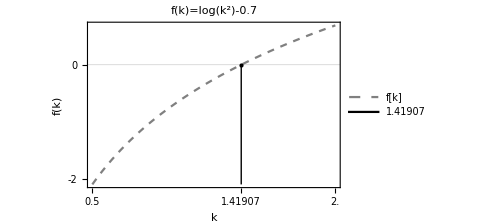
Arguments
func | {x_l,x_u} | steps
Log[#1^2]-0.7& | {0.5,2.} | MaxSteps→3
Part A
-Graphics-
Parts B,C
Bisection | 1.625
FalsePosition | 1.49701n = 3Problem 5.7

```mathematica
DisplayColumn["Problem 5.7",
{"Arguments","Part A","Parts B,C"},{
Out[7],Out[5],Out[8]}]
```

### 5.16 Doping Density Dependence on Desired Resistivity

The resistivity ρ of doped silicon is based on the charge q of an electron, the electron density n, and the electron mobility μ. The electron density is given in terms of the doping density N and the intrinsic carrier density n_i. The electron mobility is described by the temperature T, the reference temperature T_0, and the reference mobility μ_0.

Resistivity | ρ
Desired  resistivity | ρ_d
Charge | q
ℯ density | 𝓃
Doping density | 𝒩
Intr. carr. density | 𝓃_i
Temp | T
Ref Temp | T_0

#### Code

```mathematica
Clear["Global`*"]
```

```mathematica
$Line=0;
```

```mathematica
(* Variables *)
{Tref,Ta,μ0,q,ni,ρd}={300.,1000.,1360.,1.7 10^(-19),6.21 10^9,6.5 10^6};
{𝒩[l],𝒩[u]}={0.,2.5 10^(10)};
```

```mathematica
(* Functions *)
ρ[q_,𝒩_,μ_]:= 1/(q  n[𝒩] μ);
```

```mathematica
n[𝒩_]:=0.5(𝒩 + √(𝒩^2 +4ni^2));
```

```mathematica
μ=μ0*(Ta/Tref)^(-2.42);
```

```mathematica
NSolve[ρ[q,𝒩,μ]==ρd,𝒩][[1]];
```

```mathematica
(* RHS == 0 *)
f=(ρ[q,#,μ]-ρd)&;
```

```mathematica
Bisection[##]&@@{f,{𝒩[l],𝒩[u]}};
```

```mathematica
FalsePosition[##]&@@{f,{𝒩[l],𝒩[u]}};
```

#### Output

```mathematica
DisplayColumn["Problem 5.16",{"Mathematica NSolve","Bisection","FalsePosition"},{𝒩/.Out[6],Out[8],Out[9]}]
```

Mathematica NSolve
9.11359×10^9
Bisection
9.13086×10^9
FalsePosition
9.11809×10^9Problem 5.16

### 5.22 Sphere in Water Equilibrium

To solve for the height above water of the sphere, the buoyant and gravitational forces must reach equilibrium. Thus, to find the solution of the height above water, equate the equations below and solve for the root as a function of <h>. Note that, h ∈[0,2]. The ball can be completely submerged h=0, no submergence h=2r = 2, or some value in the interval.

F_b=ρ_w V_sub g = ρ_w(4/3 π r^3-(π h^2)/3(3r-h))g

F_g=ρ_s V_s g=ρ_s(4/3 π r^3)g

#### Code

```mathematica
Clear["Global`*"]; $Line=0;
```

```mathematica
(* Constants *)
{g,ρ[w],ρ[s],rad}={9.8,1000,200,1};
```

```mathematica
(* Force Gravity (x^- direction) *)
FG[r_,ρ_]:=Vs[r]ρ g
```

```mathematica
(* Force Bouyant (x^+ direction) *)
FB[r_]:=(Vsub[r] ρ[w]g)
```

```mathematica
(* Volume of Sphere *)
Vs[r_]:=4/3 π r^3
```

```mathematica
(* Volume above surface *)
Vd[r_]:=(π h^2/3 (3r-h))
```

```mathematica
(* Volume below surface *)
Vsub[r_]:=Vs[r]-Vd[r]
```

```mathematica
(* Height above surface: restricing h ∈ [0,2] *)
NumberForm[h,10]/.NSolve[FB[rad]==FG[rad,ρ[s]] && 0.≤h≤2.,h][[1]];
```

```mathematica
(* Function for numerical methods *) 
f=Function[h,Evaluate[FB[1]-FG[1,ρ[s]]]];
```

```mathematica
Bisection[##]&@@{f,{0.0,2.0}}//NumberForm[#,10]&;
```

```mathematica
FalsePosition[##]&@@{f,{0.,2.}}//NumberForm[#,10]&;
```

#### Output

```mathematica
DisplayColumn["Problem 5.22",{"Mathematica NSolve","Bisection","False Position"},{Out[7],Out[9],Out[10]}]
```

Mathematica NSolve
1.425718549
Bisection
1.42578125
False Position
1.425718549Problem 5.22